# EMERGENT BIG BANG MODEL

This notebook is supplementary material for the paper
The emergent Big Bang scenario
	by Justin C. Feng*, Shinji Mukohyama and Jean-Philippe Uzan
	"arXiv:2602.02646" [gr-qc]

This notebook was written in Mathematica 14.3.

*feng@fzu.cz

### FORMAL CALCULATIONS

#### SOME DEFINITIONS

##### G4 AND SCRIPT G

```mathematica
{GS[ψs]->G4[ψs]-2 ψs G4'[ψs]};
repsGS2G4=Join[%,D[%,ψs]/.%]
```

{GS[ψs]→G4[ψs]-2 ψs G4'[ψs],GS'[ψs]→-G4'[ψs]-2 ψs G4''[ψs]}

```mathematica
GS[ψs]==(GS[ψs]/.repsGS2G4);
Solve[%,G4'[ψs]][[1]];
repsG42GS=Join[%,D[%,ψs]/.%]//FullSimplify
```

{G4'[ψs]→(G4[ψs]-GS[ψs])/(2 ψs),G4''[ψs]→-(G4[ψs]-GS[ψs]+2 ψs GS'[ψs])/(4 ψs^2)}

#### EQUATIONS

##### ORIGINAL SYSTEM

```mathematica
Eq1GSK=-J0/(√ψs aE[ψs]^3)+6 HE[ψs]^2 GS'[ψs]+KE'[ψs];
Eq2GSK=-(2 J0 √ψs)/aE[ψs]^3-6 GS[ψs] HE[ψs]^2+KE[ψs];
```

##### ALGEBRAIC RELATIONS

DERIVATION

```mathematica
{Eq1GSK==0,Eq2GSK==0}/.{aE[ψs]->x^(1/3)}/.{HE[ψs]->y^(1/2)};
repsalgrelsxy=Solve[%,{x,y}][[1]];
repsalgrels=repsalgrelsxy/.{x->aE[ψs]^3,y->HE[ψs]^2}//FullSimplify
```

{aE[ψs]^3→(J0 (GS[ψs]+2 ψs GS'[ψs]))/(√ψs (KE[ψs] GS'[ψs]+GS[ψs] KE'[ψs])),HE[ψs]^2→(KE[ψs]-2 ψs KE'[ψs])/(6 GS[ψs]+12 ψs GS'[ψs])}

##### EXTRACTING DYNAMICS

RELATION BETWEEN A CUBED AND H

```mathematica
D[aE[z]^3,z]/aE[z]^3==3HE[z]
```

(3 aE'[z])/aE[z]==3 HE[z]

```mathematica
D[Log[aE[z]^3],z]
```

(3 aE'[z])/aE[z]

FINDING PSI DOT

```mathematica
D[Log[a3E[ψ[z]^2]],z]//FullSimplify;
%==3HE[ψ[z]^2];
repspsidotdisp=Solve[%,ψ'[z]][[1]]
```

{ψ'[z]→(3 a3E[ψ[z]^2] HE[ψ[z]^2])/(2 ψ[z] a3E'[ψ[z]^2])}

```mathematica
D[Log[x/.repsalgrelsxy/.{ψs->ψ[z]^2}],z]//FullSimplify;
%==3HE[ψs];
Solve[%,ψ'[z]][[1]]/.{ψ[z]->XE^(1/2),ψs->XE}//FullSimplify;
repspsidotraw=%/.{HE[XE]->((KE[XE]-2 ψs KE'[XE])/(6 GS[XE]+12 ψs GS'[XE]))^(1/2)}/.{ψs->XE}//FullSimplify;
```

H DOT

```mathematica
D[HE[ψ[z]^2],z]/.repspsidotdisp

%-(3 a3E[ψ[z]^2])/2(D[HE[x] ^2,x]/.{x->ψ[z]^2})/a3E'[ψ[z]^2]
```

(3 a3E[ψ[z]^2] HE[ψ[z]^2] HE'[ψ[z]^2])/a3E'[ψ[z]^2]

0

### PLOTS

#### MIRROR UNIVERSE (NUMERICAL)

##### NUMERICAL SOLUTION, LINEAR G4

FORM FOR G4

```mathematica
repslinGquadK0={G4[XE]->g0+g1 XE,KE[XE]->k0+k2/2(XE-X0)^2};
repslinGquadK1=repslinGquadK0/.{XE->ψs};
repslinGquadKs1=Join[%,D[%,ψs],D[%,{ψs,2}]];
repslinGquadKs0=repslinGquadKs1/.{ψs->XE};
```

```mathematica
G4'[ψs]==(G4'[ψs]/.repsG42GS);
Solve[%,GS[ψs]][[1]]
%/.repslinGquadKs1
repsGSlinGquadKs1=Join[%,D[%,ψs],D[%,{ψs,2}],{repslinGquadKs1[[2]],repslinGquadKs1[[4]],repslinGquadKs1[[6]]}];
repsGSlinGquadKs0=repsGSlinGquadKs1/.{ψs->XE};
```

{GS[ψs]→G4[ψs]-2 ψs G4'[ψs]}

{GS[ψs]→g0-g1 ψs}

PARAMETERS

```mathematica
repsparsmirlin={g0->1,g1->-1,k0->1,k2->-1.55,X0->1,J0->1};
```

##### EQUATIONS

RHS OF EQUATION

```mathematica
repspsidotraw/.repsGSlinGquadKs0//Simplify;
%/.{XE->ψ[z]^2};
repspsidot=FullSimplify[%,Assumptions->{ψ[z]>0,g0-3 g1 ψ[z]^2>0}];
repspsidotrhsmirlin=ψ'[z]/.%
```

(√3 ψ[z] √((g0-3 g1 ψ[z]^2) (2 k0+k2 X0^2+2 k2 X0 ψ[z]^2-3 k2 ψ[z]^4)) (2 g1 k0+2 g0 k2 X0+g1 k2 X0^2-2 k2 (g0+2 g1 X0) ψ[z]^2+3 g1 k2 ψ[z]^4))/(-2 g0 (2 g1 k0+2 g0 k2 X0+g1 k2 X0^2)+6 ψ[z]^2 (2 g0^2 k2+2 g0 g1 k2 X0-g1^2 (2 k0+k2 X0^2)+g1 k2 ψ[z]^2 (-7 g0-4 g1 X0+9 g1 ψ[z]^2)))

ZERO

```mathematica
repszero={ψ0->√((k2 X0-√2 √(k2 (3 k0+2 k2 X0^2)))/(3 k2))};
```

```mathematica
repspsidotrhsmirlin/.{ψ[z]->ψ0}/.repszero//Simplify
```

0

POSITIVITY OF ALGEBRAIC RELATIONS

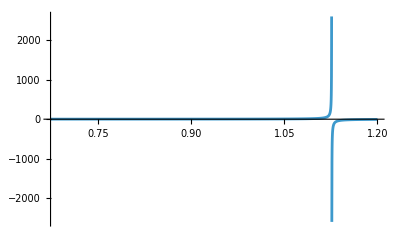

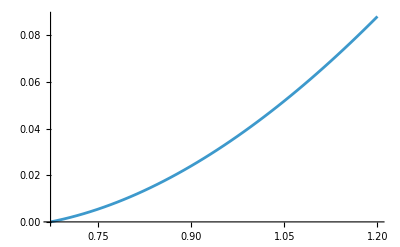

```mathematica
x/.repsalgrelsxy/.repsGSlinGquadKs1;
FullSimplify[(%/.{ψs->q^2}),Assumptions->{q>0}];
%/.repsparsmirlin;
Plot[%,{q,(ψ0/.repszero/.repsparsmirlin),1.2},PlotRange->All]
y/.repsalgrelsxy/.repsGSlinGquadKs1;
FullSimplify[(%/.{ψs->q^2}),Assumptions->{q>0}];
%/.repsparsmirlin;
Plot[%,{q,(ψ0/.repszero/.repsparsmirlin),1.2}]
```

##### SOLVE

SOLVE FOR PSI

{ψ[z]→InterpolatingFunction[…][z]}

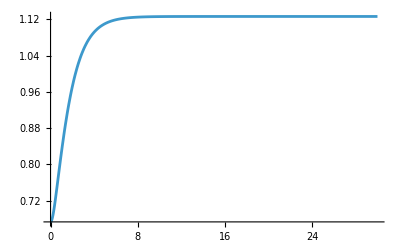

```mathematica
repspsidotrhsmirlin/.repsparsmirlin;
{ψ'[z]==%,ψ[0]==(ψ0/.repszero/.repsparsmirlin)};
repspsisolna=NDSolve[%,ψ[z],{z,0,30}][[1]]
psizsolna=(ψ[z]/.%);
psizsolnaF[zF_]:=psizsolna/.{z->zF};
Plot[psizsolnaF[zF],{zF,0,30},PlotRange->All]
```

{ψ[z]→InterpolatingFunction[…][z]}

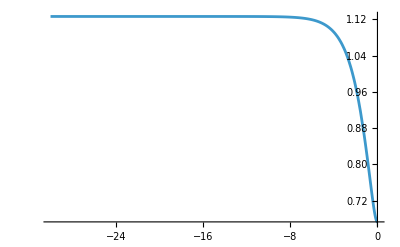

```mathematica
repspsidotrhsmirlin/.repsparsmirlin;
{ψ'[z]==%,ψ[0]==-(ψ0/.repszero/.repsparsmirlin)};
repspsisolnb=NDSolve[%,ψ[z],{z,0,30}][[1]]
psizsolnb=-(ψ[z]/.%);
psizsolnbF[zF_]:=psizsolnb/.{z->-zF};
Plot[psizsolnbF[zF],{zF,-30,0},PlotRange->All]
```

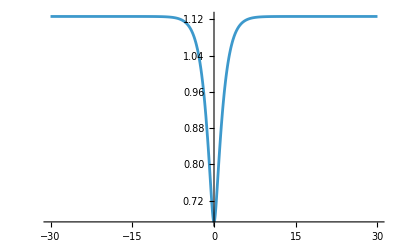

```mathematica
psizsol[x_]:=Piecewise[{{psizsolnaF[x],x>0},{psizsolnbF[x],x<0}}];
psol=Plot[psizsol[zz],{zz,-30,30},PlotRange->All]
```

CONSTRUCT A AND H

```mathematica
x/.repsalgrelsxy/.repsGSlinGquadKs1/.{ψs->ψ[z]^2}/.repsparsmirlin/.{ψ[z]->0.7}
```

1.78547

```mathematica
x/.repsalgrelsxy/.repsGSlinGquadKs1/.{ψs->ψ[z]^2};
aE3Formpars=FullSimplify[%,Assumptions->{ψ[z]>0}];
aEFormpars=Simplify[aE3Formpars^(1/3)];

aE3parsF[zF_]:=aE3Formpars/.repsparsmirlin/.repspsisolna/.{z->zF};

aEparsF[zF_]:=aEFormpars/.repsparsmirlin/.repspsisolna/.{z->zF};
```

```mathematica
aEsol[x_]:=Piecewise[{{aEparsF[x],x>0},{aEparsF[-x],x<0}}];
```

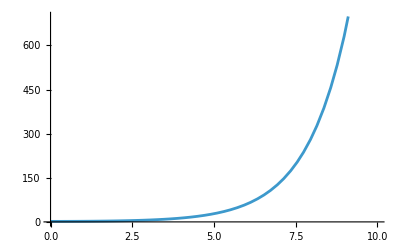

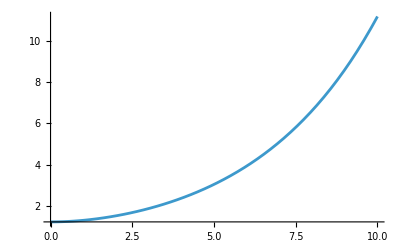

```mathematica
Plot[aE3parsF[zz],{zz,0,10}]
Plot[aEparsF[zz],{zz,0,10}]
```

```mathematica
y/.repsalgrelsxy/.repsGSlinGquadKs1/.{ψs->ψ[z]^2};
Simplify[%,Assumptions->{ψ[z]>0}];
HEFormpars=%^(1/2);
HEparsFa[zF_]:=HEFormpars/.repsparsmirlin/.repspsisolna/.{z->zF};
HEparsFb[zF_]:=-HEFormpars/.repsparsmirlin/.repspsisolnb/.{z->-zF};
```

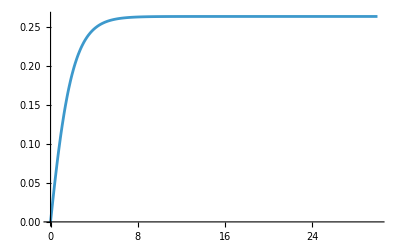

```mathematica
pHE=Plot[HEparsFa[zz],{zz,0,30},PlotRange->All]
```

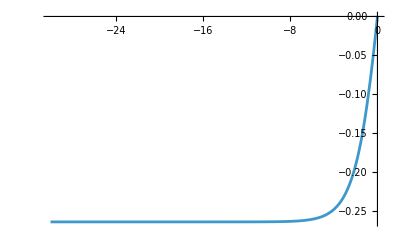

```mathematica
Plot[HEparsFb[zz],{zz,-30,0},PlotRange->All]
```

InterpolatingFunction::dmval: Input value {-29.9988} lies outside the range of data in the interpolating function. Extrapolation will be used.

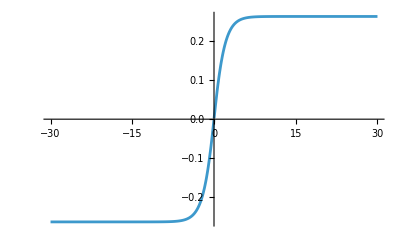

```mathematica
Hzsol[x_]:=Piecewise[{{HEparsFa[x],x>0},{HEparsFb[x],x<0}}];
pHsol=Plot[Hzsol[zz],{zz,-30,30},PlotRange->All]
```

VALIDATION - CHECKING DERIVATIVES OF GH

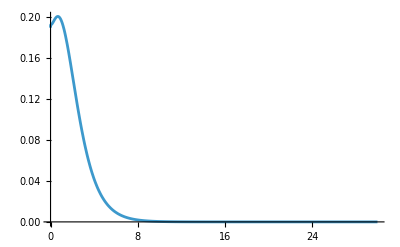

```mathematica
(* ANALYTIC DERIVATIVE OF GH *)
D[(1+psizsolnaF[z]^2)HEparsFa[z],z];
pRC1=Plot[%,{z,0,30},PlotRange->All]
```

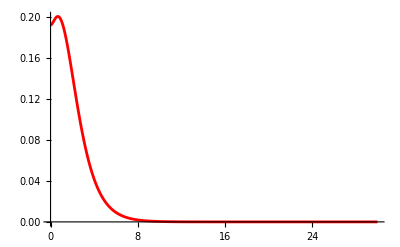

```mathematica
(* NUMERICAL DERIVATIVE OF GH *)
1/2 psizsolnaF[zz]/aE3parsF[zz];
pRC2=Plot[%,{zz,0,30},PlotStyle->Red,PlotRange->All]
```

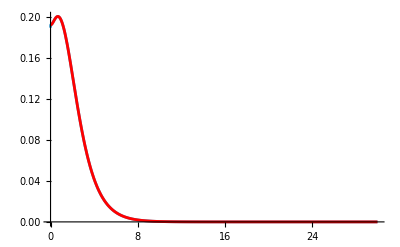

```mathematica
(* COMPARISON *)
Show[pRC1,pRC2]
```

##### PLOTS

OPTIONS

```mathematica
goldenRatio=(1+Sqrt[5])/2;
prdPlotOptionsPhase={Frame->True,FrameStyle->Directive[Black,22],AspectRatio->1/goldenRatio,ImageSize->400,BaseStyle->{FontFamily->"Times",FontSize->22},PlotRange->{{-1.5,1.5},{-1.49,1.49}},FrameLabel->{Style["ψ",30]},LabelStyle->Directive[Black,FontFamily->"Times"]};
```

```mathematica
prdPlotOptionssol={Frame->True,FrameStyle->Directive[Black,22],AspectRatio->1/goldenRatio,ImageSize->400,BaseStyle->{FontFamily->"Times",FontSize->12},PlotRange->{{-10,10},{-0.5,1.5}},FrameLabel->{Style["z",24]},LabelStyle->Directive[Black,FontFamily->"Times"]};
```

PLOTS - PHASE

```mathematica
(* HE^2 *)
(HE[ψs]^2/.repsalgrels)/.repsGSlinGquadKs1/.{ψs->x^2, ψ[z]->x}/.repsparsmirlin;
HEsPx=10FullSimplify[%,Assumptions->{x>0}]
```

(10 (0.0125-0.0861111 x^2+0.129167 x^4))/(0.333333+1. x^2)

```mathematica
(* aE^3 *)
(aE[ψs]^3/.repsalgrels)/.repsGSlinGquadKs1/.{ψs->x^2, ψ[z]->x}/.repsparsmirlin;
aE3Px=FullSimplify[%,Assumptions->{x>0}]
```

(0.430108+1.29032 x^2)/(0.763441 x+0.666667 x^3-1. x^5)

```mathematica
PltLinG4algphase=Plot[{HEsPx,1/aE3Px},{x,-1.5,1.5},Evaluate[prdPlotOptionsPhase],PlotStyle->{{Thick,Black},{Thick,Black,Dashed}},PlotLegends->Placed[LineLegend[Automatic,{"10H_E^2","a^-3"},LegendFunction->"Panel", LabelStyle->Directive[FontFamily->"Times",FontSize->20],LegendMarkerSize->18],{0.70,0.22}]];
Export["LinG4algphase.pdf",PltLinG4algphase];

PltLinG4algphaseNL=Plot[{HEsPx,1/aE3Px},{x,-1.5,1.5},Frame->True,FrameStyle->Directive[Black,22],AspectRatio->1/goldenRatio,ImageSize->400,BaseStyle->{FontFamily->"Times",FontSize->22},PlotRange->{{-1.5,1.5},{-1.4,1.4}},LabelStyle->Directive[Black,FontFamily->"Times"],FrameTicks->{{Automatic,Automatic},{None,Table[{i,""},{i,-3,3,0.1}]}},PlotStyle->{{Thick,Black},{Thick,Black,Dashed}},PlotLegends->Placed[LineLegend[Automatic,{"10H_E^2","a^-3"},LegendFunction->"Panel", LabelStyle->Directive[FontFamily->"Times",FontSize->20],LegendMarkerSize->18],{0.70,0.22}]];
```

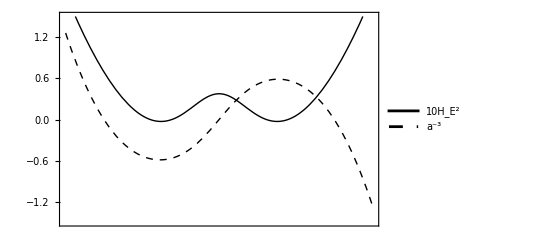

```mathematica
PltLinG4algphaseNL=Plot[{HEsPx,1/aE3Px},{x,-1.5,1.5},Frame->True,FrameStyle->Directive[Black,22],AspectRatio->1/goldenRatio,ImageSize->400,BaseStyle->{FontFamily->"Times",FontSize->22},PlotRange->{{-1.5,1.5},{-1.49,1.5}},LabelStyle->Directive[Black,FontFamily->"Times"],FrameTicks->{{Automatic,Automatic},{(*Bottom axis:two-sided ticks*)Join[Table[{i,"",{0.002,0.002}},{i,-1.5,1.5,0.1}],(*Minor ticks*)Table[{i,"",{0.008,0.008}},{i,-1.5,1.5,0.5}]   (*Major ticks*)],(*Top axis:one-sided ticks (inward only)*)Join[Table[{i,"",{0.002,0}},{i,-1.5,1.5,0.1}],(*Minor ticks*)Table[{i,"",{0.008,0}},{i,-1.5,1.5,0.5}]   (*Major ticks*)]}},PlotStyle->{{Thick,Black},{Thick,Black,Dashed}},PlotLegends->Placed[LineLegend[Automatic,{"10H_E^2","a^-3"},LegendFunction->"Panel",LabelStyle->Directive[FontFamily->"Times",FontSize->20],LegendMarkerSize->18],{0.70,0.22}]]
```

```mathematica
(* ψ̇/HE *)
(3(aE[ψs]^3/.repsalgrels))/(2ψ D[(aE[ψs]^3/.repsalgrels),ψs]);
%/.repsGSlinGquadKs1/.{ψs->ψ^2}/.{ ψ->x}/.repsparsmirlin;
dotpsiPx=FullSimplify[%,Assumptions->{x>0}]
```

(0.25448 x+0.985663 x^3+0.333333 x^5-1. x^7)/(-0.0848268+0.0322581 x^2+0.333333 x^4+1. x^6)

```mathematica
(* Ḣ E *)
(3(aE[ψs]^3/.repsalgrels))/2 D[(HE[ψs]^2/.repsalgrels),ψs]/D[(aE[ψs]^3/.repsalgrels),ψs]/.repsGSlinGquadKs1/.{ψs->ψ^2}/.{ ψ->x}/.repsparsmirlin;
dotHEPx=FullSimplify[%,Assumptions->{x>0}]
```

(x^2 (-0.0314566+0.0382716 x^2+0.197222 x^4+2.77556×10^-17 x^6-0.129167 x^8))/(-0.0282756-0.0740741 x^2+0.143369 x^4+0.666667 x^6+1. x^8)

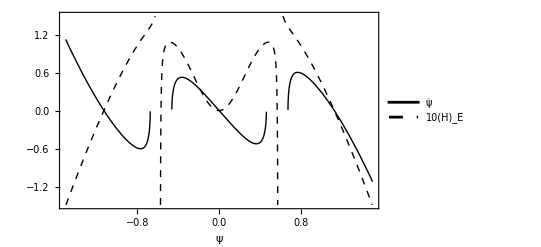

```mathematica
PltLinG4dotphase=Plot[{dotpsiPx Sqrt[Sign[HEsPx]]Sqrt[Abs[HEsPx]],10dotHEPx },{x,-1.5,1.5},Evaluate[prdPlotOptionsPhase],PlotStyle->{{Thick,Black},{Thick,Black,Dashed}},PlotLegends->Placed[LineLegend[Automatic,{"ψ̇","10(Ḣ)_E"},LegendFunction->"Panel", LabelStyle->Directive[FontFamily->"Times",FontSize->20],LegendMarkerSize->18],{0.16,0.76}]]
Export["LinG4dotphase.pdf",PltLinG4dotphase];

PltLinG4dotphaseNL=Plot[{dotpsiPx Sqrt[Sign[HEsPx]]Sqrt[Abs[HEsPx]],10dotHEPx },{x,-1.5,1.5},Evaluate[prdPlotOptionsPhase],FrameTicks->{{Automatic,Automatic},{Automatic,None}},PlotStyle->{{Thick,Black},{Thick,Black,Dashed}},PlotLegends->Placed[LineLegend[Automatic,{"ψ̇","10(Ḣ)_E"},LegendFunction->"Panel", LabelStyle->Directive[FontFamily->"Times",FontSize->20],LegendMarkerSize->18],{0.16,0.76}]];
```

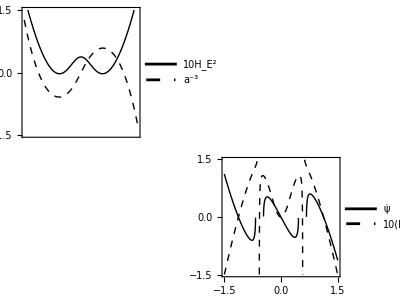

```mathematica
PlotsStackedPhase=Graphics[{Inset[PltLinG4algphaseNL,{-0.0180,0.709},{Center,Center},Scaled[{0.964,0.964}]],Inset[PltLinG4dotphaseNL,{0,0.1},{Center,Center},Scaled[{0.99995,0.99995}]]},PlotRange->{{-0.5,0.5},{-0.3,1}},ImageSize->400]
Export["LinG4phase.pdf",PlotsStackedPhase];
```

PLOTS - SOLUTION

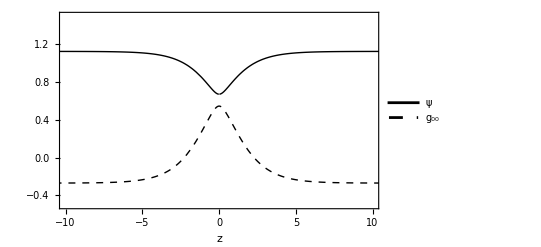

InterpolatingFunction::dmval: Input value {-29.9988} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

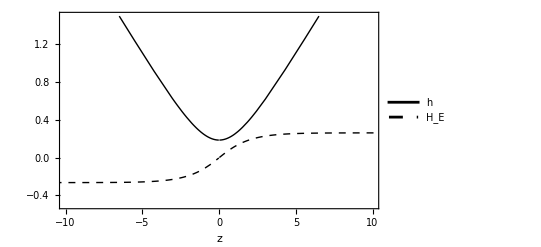

```mathematica
plpsisol=Plot[{psizsol[zz],(1-psizsol[zz]^2/M^4/.{M->1})},{zz,-30,30},Evaluate[prdPlotOptionssol],PlotStyle->{{Thick,Black},{Thick,Black,Dashed}},PlotLegends->Placed[LineLegend[Automatic,{"ψ","g_00"},LegendFunction->"Panel", LabelStyle->Directive[FontFamily->"Times",FontSize->22],LegendMarkerSize->20],{Left,Center}]]
Export["LinG4psisoln.pdf",plpsisol];
plhHEsols=Plot[{Log[aEsol[zz]],Hzsol[zz]},{zz,-30,30},Evaluate[prdPlotOptionssol],PlotStyle->{{Thick,Black},{Thick,Black,Dashed}},PlotLegends->Placed[LineLegend[Automatic,{"h","H_E"},LegendFunction->"Panel", LabelStyle->Directive[FontFamily->"Times",FontSize->22],LegendMarkerSize->20],{Left,Center}]]
Export["LinG4Hsoln.pdf",plhHEsols];
```

```mathematica
plpsisolNL=Plot[{psizsol[zz],(1-psizsol[zz]^2/M^4/.{M->1})},{zz,-30,30},Frame->True,FrameStyle->Directive[Black,22],AspectRatio->1/goldenRatio,ImageSize->400,BaseStyle->{FontFamily->"Times",FontSize->12},PlotRange->{{-10,10},{-0.4,1.5}},LabelStyle->Directive[Black,FontFamily->"Times"],FrameTicks->{{Automatic,Automatic},{(*Bottom axis:two-sided ticks*)Join[Table[{i,"",{0.002,0.002}},{i,-10,10,1}],(*Minor ticks*)Table[{i,"",{0.008,0.008}},{i,-10,10,5}]   (*Major ticks*)],(*Top axis:one-sided ticks (inward only)*)Join[Table[{i,"",{0.002,0}},{i,-10,10,1}],(*Minor ticks*)Table[{i,"",{0.008,0}},{i,-10,10,5}]   (*Major ticks*)]}},PlotStyle->{{Thick,Black},{Thick,Black,Dashed}},PlotStyle->{{Thick,Black},{Thick,Black,Dashed}},PlotLegends->Placed[LineLegend[Automatic,{"ψ","g_00"},LegendFunction->"Panel", LabelStyle->Directive[FontFamily->"Times",FontSize->22],LegendMarkerSize->20],{Left,Center}]];

plhHEsolsST=Plot[{Log[aEsol[zz]],Hzsol[zz]},{zz,-30,30},Frame->True,FrameStyle->Directive[Black,22],AspectRatio->1/goldenRatio,ImageSize->400,BaseStyle->{FontFamily->"Times",FontSize->12},PlotRange->{{-10,10},{-0.5,1.4}},FrameTicks->{{Automatic,Automatic},{Automatic,None}},LabelStyle->Directive[Black,FontFamily->"Times"],FrameLabel->{Style["z",30]},PlotStyle->{{Thick,Black},{Thick,Black,Dashed}},PlotLegends->Placed[LineLegend[Automatic,{"h","H_E"},LegendFunction->"Panel", LabelStyle->Directive[FontFamily->"Times",FontSize->22],LegendMarkerSize->20],{Left,Center}]];
```

InterpolatingFunction::dmval: Input value {-29.9988} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

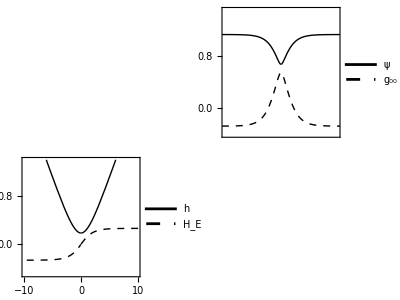

```mathematica
PlotsStackedSol=Graphics[{Inset[plpsisolNL,{0.0028,0.7135},{Center,Center},Scaled[{0.9367,0.9367}]],Inset[plhHEsolsST,{0,0.1},{Center,Center},Scaled[{0.99995,0.99995}]]},PlotRange->{{-0.5,0.5},{-0.3,1}},ImageSize->400]
Export["LinG4sol.pdf",PlotsStackedSol];
```

APPROXIMATE SOLUTION

```mathematica
1.135+ep-1==0.54;
Solve[%,ep]
```

{{ep→0.405}}

```mathematica
1.135-0.46 1/(1+(z/1.4)^2)/.{z->0}
```

0.675

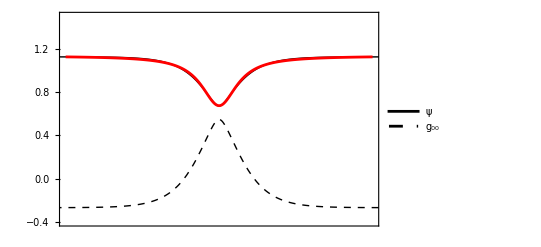

```mathematica
ppsiapx=Plot[1.135-0.46 1/(1+(z/1.4)^2),{z,-10,10},PlotStyle->Red,PlotRange->{{-10,10},{-0.5,1.5}}];
Show[plpsisolNL,ppsiapx]
```

```mathematica
D[ArcTan[x],x]
```

1/(1+x^2)

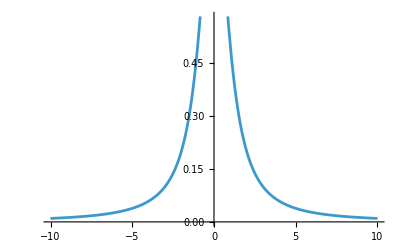

```mathematica
Plot[1/(1+x^2),{x,-10,10}]
```

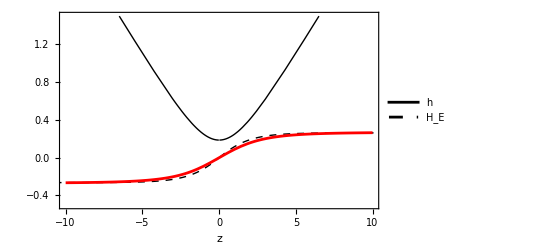

```mathematica
pHEapx=Plot[(2 k ((k z)/(1+k^2 z^2)+ArcTan[k z]))/π/.{k->0.27},{z,-10,10},PlotStyle->Red,PlotRange->{{-10,10},{-0.5,1.5}}];
Show[plhHEsols,pHEapx]
```

##### SCRATCHWORK

RANDOM INTEGRATION SCRIPT

```mathematica
NIntegrateODEnum[f_,x0_,xf_]:=Module[{IDef,x},IDef[x]/.NDSolve[{IDef'[x]==f[x],IDef[x0]==0},IDef[x],{x,x0,xf}][[1]]/.{x->xf}
];
```

```mathematica
NIntegrateODE[f_,x_,x0_,xf_]:=Module[{IDef},IDef[x]/.NDSolve[{IDef'[x]==f[x],IDef[x0]==0},IDef[x],{x,x0,xf}][[1]]
];
```

```mathematica
FF[x_]:=2x;
NIntegrateODE[FF,x,0,10]
```

InterpolatingFunction[…][x]

#### RECONSTRUCTION

##### FUNCTIONS

RECONSTRUCT G FUNCTIONS

```mathematica
(* Somehow, NIntegrate is broken on my version of Mathematica (14.1.0.0), so I use NDSolve here. *)
```

```mathematica
GHreco[zF_,zmax_,ψ_,aE_]:=Module[{GH,zz,Fret},GH[zz]/.NDSolve[{GH'[zz]==(ψ[zz]/aE[zz]^3),GH[0]==0},GH[zz],{zz,0,zmax}][[1]]/.{zz->zF}];

GSreco[zF_,zmax_,C0_,J0_,ψ_,aE_,HE_,eps_]:=Module[{},(C0+J0 GHreco[zF,zmax,ψ,aE]/2)/(HE[zF]+eps)];

KSreco[zF_,zmax_,C0_,J0_,ψ_,aE_,HE_,eps_]:=Module[{},(6 HE[zF]^2 GSreco[zF,zmax,C0,J0,ψ,aE,HE,eps]+2 J0 (ψ[zF]/aE[zF]^3))];

G4reco[zF_,zmax_,C0_,J0_,ψ_,aE_,HE_,eps_]:=Module[{Gd,zz,dpsi},
dpsi=D[ψ[zz],zz];ψ[zz]Gd[zz]/.NDSolve[{(Gd'[zz]==(-GSreco[zz,zmax,C0,J0,ψ,aE,HE,eps])(dpsi/ψ[zz]^2)),Gd[0]==0},Gd[zz],{zz,0,zmax}][[1]]/.{zz->zF}];
```

```mathematica
GSreconi[zF_,zmax_,C0_,J0_,ψ_,aE_,HE_,eps_]:=(C0+J0 GHreco[zF,zmax,ψ,aE]/2)/(HE[zF]+eps);

KSreconi[zF_,zmax_,C0_,J0_,ψ_,aE_,HE_,eps_]:=(6 HE[zF]^2 GSreco[zF,zmax,C0,J0,ψ,aE,HE,eps]+2 J0 (ψ[zF]/aE[zF]^3));

G4reconi[zF_,zmax_,C0_,J0_,ψ_,aE_,HE_,eps_]:=Module[{zz,dpsi},
dpsi=D[ψ[zz],zz];ψ[zF]NIntegrate[(-GSreco[zz,zmax,C0,J0,ψ,aE,HE,eps])(dpsi/ψ[zz]^2),{zz,0,zF}, AccuracyGoal->.1]];
```

```mathematica
GSnmirror[zF_ ?NumberQ]:=GSreco[zF,30,0,1,psizsolnaF,aEparsF,HEparsFa,0]
KSnmirror[zF_ ?NumberQ]:=KSreco[zF,30,0,1,psizsolnaF,aEparsF,HEparsFa,0]
G4nmirror[zF_ ?NumberQ]:=G4reco[zF,30,0,1,psizsolnaF,aEparsF,HEparsFa,0]
```

##### CHECKING RECONSTRUCTION FROM NUMERICAL SOLUTION

RECONSTRUCT G and G4

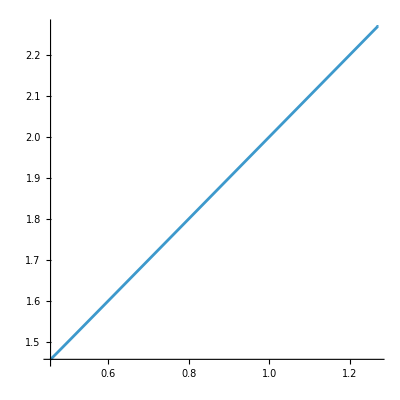

```mathematica
pGSn=ParametricPlot[{psizsolnaF[zz]^2,GSnmirror[zz]},{zz,0.1,29.9},PlotRange->All,AspectRatio->1]
```

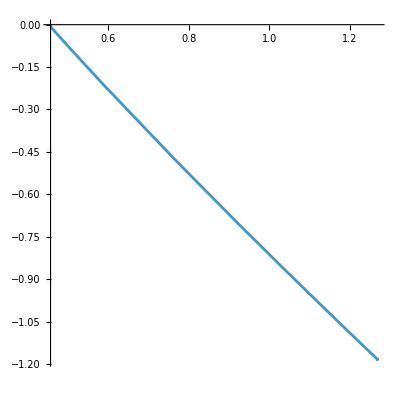

```mathematica
pG4n=ParametricPlot[{psizsolnaF[zz]^2,G4nmirror[zz]},{zz,0.1,29.9},PlotRange->All,AspectRatio->1]
```

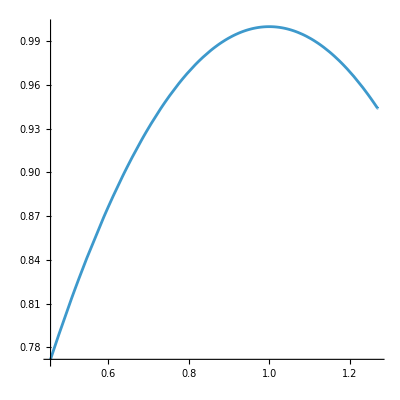

```mathematica
pKSn=ParametricPlot[{psizsolnaF[zz]^2,KSnmirror[zz]},{zz,0.1,29.9},PlotRange->All,AspectRatio->1]
```

CHECKING RECONSTRUCTION

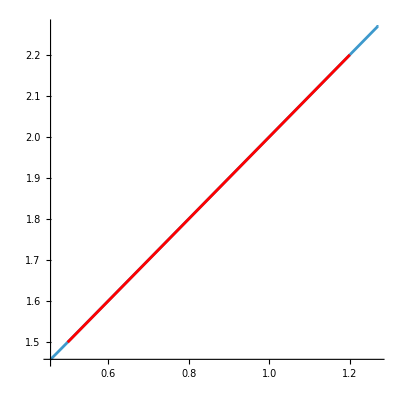

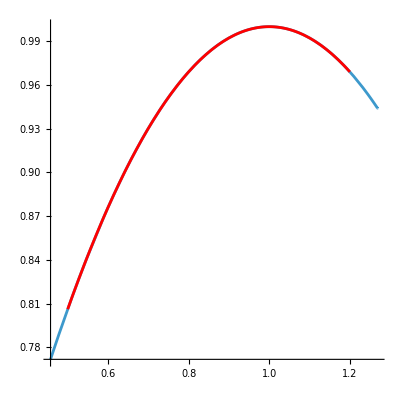

```mathematica
(* RED IS THE ANSATZ, BLUE IS THE RECONSTRUCTION *)

Show[pGSn,Plot[(g0-g1 ψs/.repsparsmirlin),{ψs,0.5,1.2},PlotStyle->Red]]
Show[pKSn,Plot[(k0+1/2 k2 (-X0+ψs)^2/.repsparsmirlin),{ψs,0.5,1.2},PlotStyle->Red]]
```

##### RECONSTRUCTING MIRROR AND POCKET UNIVERSES

INPUT FUNCTIONS

```mathematica
Mpl=.7;           (* mass scale for g00 *)
```

```mathematica
repsparsrcanz={ep->0.01}
```

{ep→0.01}

```mathematica
HErcF[xz_]:=((2 xz)/(π (1+xz^2))+(2 ArcTan[xz])/π);
hErcF[xz_]:=(2xz ArcTan[xz]/π);
aErcF[xz_]:=Exp[hErcF[xz]];
```

```mathematica
D[ Exp[-xz^2],xz]
```

-2 ⅇ^(-xz^2) xz

```mathematica
1.135-0.405
```

0.73

```mathematica
psiAF[xz_]:=1.135-0.405Exp[-xz^2];
dpsiAF[xz_]:=2 ⅇ^(-xz^2) xz;
XAF[xz_]:=psiAF[xz]^2;
g00AF[xz_,xM_]:=1-XAF[xz]/xM^4;
```

```mathematica
psiBF[xz_]:=Exp[-xz^2]/.repsparsrcanz;
dpsiBF[xz_]:=-2 ⅇ^(-xz^2) xz;
XBF[xz_]:=psiBF[xz]^2;
g00BF[xz_,xM_]:=1-XBF[xz]/xM^4;
```

SOLUTION PLOTS

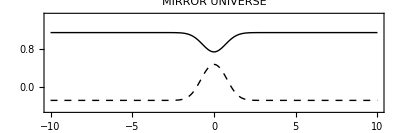

```mathematica
prdPlotOptionsnoticks={Frame->True,FrameStyle->Directive[Black,19],AspectRatio->1/3,ImageSize->400,BaseStyle->{FontFamily->"Times",FontSize->22},LabelStyle->Directive[Black,FontFamily->"Times"],FrameTicks->{{None,None},{None,None}}};

(*Mirror universes plot*)
piA=Plot[{psiAF[z],g00AF[z,1.0]},{z,-10,10},Evaluate[prdPlotOptionsnoticks],PlotRange->{{-10,10},{-0.5,1.5}},FrameLabel->{Style["z/z_*",30]},
PlotLabel->Style["MIRROR UNIVERSE",28,FontFamily->"Lato"],PlotStyle->{{Thick,Black},{Thick,Black,Dashed}},PlotLegends->Placed[LineLegend[Automatic,{"ψ","g_00"},LegendFunction->"Panel",LabelStyle->Directive[FontFamily->"Times",FontSize->19],LegendMarkerSize->17],{0.105,0.49}]]

Export["FigSol1A.pdf",piA];
```

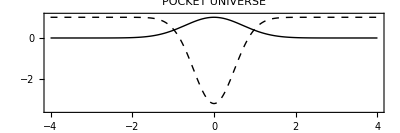

```mathematica
piB=Plot[{psiBF[z],g00BF[z,Mpl]},{z,-4,4},Evaluate[prdPlotOptionsnoticks],PlotRange->{{-4,4},{-3.5,1.1}},FrameLabel->{Style["z/z_*",30]},
PlotLabel->Style["POCKET UNIVERSE",28,FontFamily->"Lato"],PlotStyle->{{Thick,Black},{Thick,Black,Dashed}},PlotLegends->Placed[LineLegend[Automatic,{"ψ","g_00"},LegendFunction->"Panel",LabelStyle->Directive[FontFamily->"Times",FontSize->19],LegendMarkerSize->17],{0.105,0.4}]]

Export["FigSol1B.pdf",piB];
```

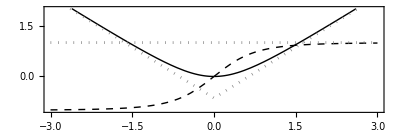

```mathematica
pGeo1=Plot[{2zz ArcTan[zz]/Pi,Abs[zz]-2/Pi,(2 zz)/(π (1+zz^2))+(2 ArcTan[zz])/π,1},{zz,-3,3},{Frame->True,FrameStyle->Directive[Black,18],AspectRatio->1/3,ImageSize->400,BaseStyle->{FontFamily->"Times",FontSize->18},PlotRange->{{-3,3},{-1.0,2.0}},LabelStyle->Directive[Black,FontFamily->"Times"]},PlotRange->{{-3,3},{-1,2}},FrameLabel->{Style["kz",15]},FrameTicks->{{None,None},{None,None}},PlotStyle->{{Thick,Black},{Gray,Dotted},{Thick,Black,Dashed},{Gray,Dotted}},PlotLegends->Placed[LineLegend[Automatic,{"h",None,"H_E",None},LegendFunction->"Panel",LabelStyle->Directive[FontFamily->"Times",FontSize->15],LegendMarkerSize->18],{0.90,0.31}]]

Export["FigSolmodelI.pdf",pGeo1];
```

RECONSTRUCTED PLOTS

```mathematica
GSrcm[zF_]:=GSreco[zF,100,0,1,psiAF,aErcF,HErcF,10^(-8)]
KSrcm[zF_]:=KSreco[zF,100,0,1,psiAF,aErcF,HErcF,10^(-8)]
G4rcm[zF_ ?NumberQ]:=G4reco[zF,100,0,5,psiAF,aErcF,HErcF,10^(-8)]
```

```mathematica
GSrcp[zF_]:=GSreconi[zF,100,0,1,psiBF,aErcF,HErcF,10^(-8)]
KSrcp[zF_]:=KSreconi[zF,100,0,1,psiBF,aErcF,HErcF,10^(-8)]
G4rcp[zF_ ?NumberQ]:=G4reconi[zF,100,0,1,psiBF,aErcF,HErcF,10^(-8)]
```

```mathematica
G4rcmni[zF_ ?NumberQ]:=Module[{zz},psiAF[zF]NIntegrate[(-GSreco[zz,100,0,1,psiAF,aErcF,HErcF,10^(-8)])(dpsiAF[zz]/psiAF[zz]^2),{zz,1,zF}, AccuracyGoal->.1]];
G4rcpni[zF_ ?NumberQ]:=Module[{zz},
psiBF[zF]NIntegrate[(-GSreco[zz,100,0,1,psiBF,aErcF,HErcF,10^(-8)])(dpsiBF[zz]/psiBF[zz]^2),{zz,1,zF}, AccuracyGoal->.1]];
```

```mathematica
plGSA=ParametricPlot[{XAF[zf],GSrcm[zf]},{zf,0,100}, PlotRange->{{0,1},{-1,1}},PlotStyle->{{Black}},AspectRatio->1];
plGSB=ParametricPlot[{XBF[zf],GSrcp[zf]},{zf,0,100} ,PlotRange->{{0,1},{-1,1}},PlotStyle->{{Black,Dashed}},AspectRatio->1];
```

```mathematica
0.46^(1/2)
```

0.678233

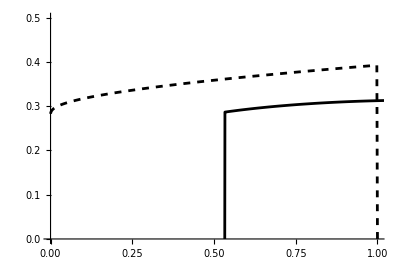

```mathematica
Show[plGSA,plGSB,PlotRange->{{0,1},{0,0.5}},AspectRatio->2/3]
```

```mathematica
plG4A=ParametricPlot[{XAF[zf],G4rcm[zf]},{zf,0,100}, PlotRange->{{0,1},{-1,1}},PlotStyle->{{Black}},AspectRatio->1];
plG4B=ParametricPlot[{XBF[zf],G4rcp[zf]},{zf,0,100} ,PlotRange->{{0,1},{-1,1}},PlotStyle->{{Black,Dashed}},AspectRatio->1];
```

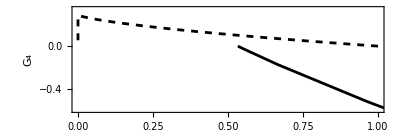

```mathematica
pG41=Show[plG4A,plG4B,Frame->True,FrameStyle->Directive[Black,14],AspectRatio->1/3,ImageSize->400,BaseStyle->{FontFamily->"Times",FontSize->14},FrameLabel->{Style["X_E",14],Style["G_4",14]},LabelStyle->Directive[Black,FontFamily->"Times"],PlotRange->{{0,1},{-.6,.35}},AspectRatio->1/3]

Export["FigmodelG41.pdf",pG41];
```

```mathematica
plG4Ani=ParametricPlot[{XAF[zf],G4rcmni[zf]},{zf,0,100}, PlotRange->{{0,1},{-1,1}},PlotStyle->{{Black}},AspectRatio->1];
plG4Bni=ParametricPlot[{XBF[zf],G4rcpni[zf]},{zf,0,100} ,PlotRange->{{0,1},{-1,1}},PlotStyle->{{Black,Dashed}},AspectRatio->1];
```

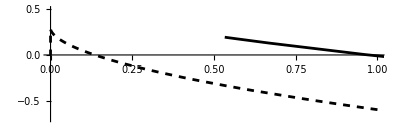

```mathematica
Show[plG4Ani,plG4Bni,PlotRange->{{0,1},{-.7,.5}},AspectRatio->1/3]
```

```mathematica
plKSA=ParametricPlot[{XAF[zF],KSrcm[zF]},{zF,0,100}, PlotRange->{{0,1},{0,3}},PlotStyle->{{Black}},AspectRatio->1];
plKSB=ParametricPlot[{XBF[zF],KSrcp[zF]},{zF,0,100} ,PlotRange->{{0,1},{0,3}},PlotStyle->{{Black,Dashed}},AspectRatio->1];
```

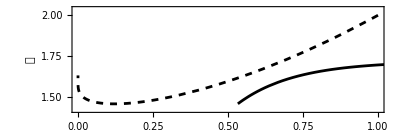

```mathematica
pK1=Show[plKSA,plKSB,Frame->True,FrameStyle->Directive[Black,14],AspectRatio->1/3,ImageSize->400,BaseStyle->{FontFamily->"Times",FontSize->14},FrameLabel->{Style["X_E",14],Style["𝒦",14]},LabelStyle->Directive[Black,FontFamily->"Times"],PlotRange->{{0,1},{1.42,2.04}},AspectRatio->1/3]

Export["FigmodelK1.pdf",pK1];
```

##### EMERGENT COSMOLOGY DYNAMICS

TIME FUNCTIONS

```mathematica
zcA0=Solve[g00AF[x,1.0]==0,x][[4]][[1]][[2]]; 
TimeAF[xz_,xM_]:=NIntegrate[Sqrt[-g00AF[y,xM]],{y,zcA0,xz}];
zcB0=Solve[g00BF[x,Mpl]==0,x][[2]][[1]][[2]]; 
TimeBF[xz_,xM_]:=NIntegrate[Sqrt[-g00BF[y,xM]],{y,-zcB0,xz}];
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

LINEAR APPROXIMATION (MIRROR)

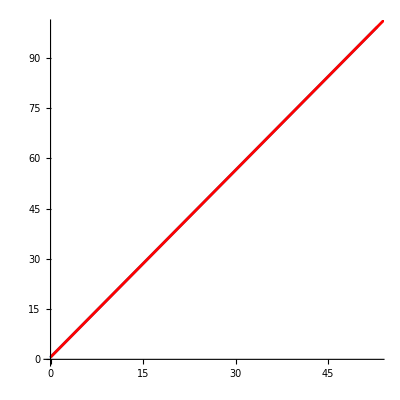

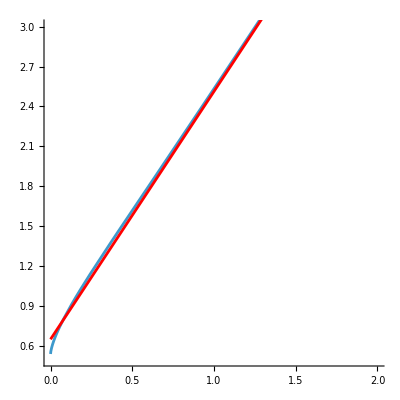

```mathematica
htlinA=1.862662520757042 t+0.6507137161844376;
atlinA=Exp[htlinA];

plhEA=ParametricPlot[{TimeAF[xxz,1.0],hErcF[xxz]},{xxz,0,100},AspectRatio->1];
Show[plhEA,Plot[htlinA,{t,0,60},PlotStyle->Red]]
Show[plhEA,Plot[htlinA,{t,0,60},PlotStyle->Red],PlotRange->{{0,2},{0.5,3}},AspectRatio->1]
```

SCALE FACTOR

```mathematica
RT1AplLP=ParametricPlot[{TimeAF[xxz,1.0],hErcF[xxz]},{xxz,zcA0,10},
Frame->True,
 FrameLabel->{"t","R"},BaseStyle->{FontFamily->"Times",FontSize->22},LabelStyle->Directive[GrayLevel[0],FontFamily->"Times"],PlotStyle->{{Black}},
PlotRange->Full,AspectRatio->1];
```

```mathematica
RT1Apl=ParametricPlot[{TimeAF[xxz,1.0],aErcF[xxz]},{xxz,zcA0,10},
Frame->True,
 FrameLabel->{"","R"},PlotStyle->{{Black}},
PlotRange->Full,AspectRatio->1];
```

```mathematica
RT1Bpl=ParametricPlot[{TimeBF[xxz,Mpl],aErcF[xxz]},{xxz,-zcB0,zcB0},
Frame->True,
 FrameLabel->{"","R"},BaseStyle->{FontFamily->"Times",FontSize->22},LabelStyle->Directive[GrayLevel[0],FontFamily->"Times"],PlotStyle->{{Black,Thick,Dashed}},
PlotRange->Full,AspectRatio->1];
```

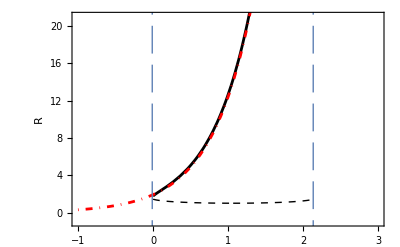

```mathematica
RT1pl0=Show[RT1Apl,RT1Bpl,Plot[atlinA,{t,-1,20},PlotStyle->{{Red,DotDashed}}],ParametricPlot[{-0.01,s},{s,-5,25},PlotStyle->{{ColorData[97,1],Thick,Dashing[{0.05,0.02}]}}],ParametricPlot[{TimeBF[zcB0,Mpl],s},{s,-5,25},PlotStyle->{{ColorData[97,1],Thick,Dashing[{0.05,0.02}]}}],BaseStyle->{FontFamily->"Times",FontSize->22},LabelStyle->Directive[GrayLevel[0],FontFamily->"Times"],PlotRange->{{-1,3},{-1,21}},Axes->False,AspectRatio->1/goldenRatio]
```

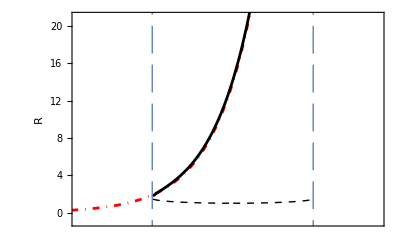

```mathematica
RT1pl0=Show[RT1Bpl,Plot[atlinA,{t,-5,20},PlotStyle->{{Red,DotDashed}}],RT1Apl,ParametricPlot[{-0.01,s},{s,-5,25},PlotStyle->{{ColorData[97,1],Thick,Dashing[{0.05,0.02}]}}],ParametricPlot[{TimeBF[zcB0,Mpl],s},{s,-5,25},PlotStyle->{{ColorData[97,1],Thick,Dashing[{0.05,0.02}]}}],BaseStyle->{FontFamily->"Times",FontSize->22},LabelStyle->Directive[GrayLevel[0],FontFamily->"Times"],PlotRange->{{-1,3},{-1,21}},FrameTicks->{{Automatic,Automatic},{(*Bottom axis:two-sided ticks*)Join[Table[{i,"",{0.002,0.002}},{i,-4,4,0.2}],(*Minor ticks*)Table[{i,"",{0.008,0.008}},{i,-4,4,1}]   (*Major ticks*)],(*Top axis:one-sided ticks (inward only)*)Join[Table[{i,"",{0.002,0}},{i,-4,4,0.2}],(*Minor ticks*)Table[{i,"",{0.008,0}},{i,-4,4,1}]   (*Major ticks*)]}},Axes->False,AspectRatio->1/goldenRatio]
```

```mathematica
RT1pl=Show[RT1Bpl,Plot[atlinA,{t,-5,20},PlotStyle->{{Red,DotDashed}}],RT1Apl,ParametricPlot[{-0.01,s},{s,-5,25},PlotStyle->{{ColorData[97,1],Thick,Dashing[{0.05,0.02}]}}],ParametricPlot[{TimeBF[zcB0,Mpl],s},{s,-5,25},PlotStyle->{{ColorData[97,1],Thick,Dashing[{0.05,0.02}]}}],BaseStyle->{FontFamily->"Times",FontSize->22},LabelStyle->Directive[GrayLevel[0],FontFamily->"Times"],PlotRange->{{-1,3},{-1,21}},FrameTicks->{{Automatic,Automatic},{(*Bottom axis:two-sided ticks*)Join[Table[{i,"",{0.002,0.002}},{i,-4,4,0.2}],(*Minor ticks*)Table[{i,"",{0.008,0.008}},{i,-4,4,1}]   (*Major ticks*)],(*Top axis:one-sided ticks (inward only)*)Join[Table[{i,"",{0.002,0}},{i,-4,4,0.2}],(*Minor ticks*)Table[{i,"",{0.008,0}},{i,-4,4,1}]   (*Major ticks*)]}},Axes->False,AspectRatio->1/goldenRatio]
```

-Graphics-

HUBBLE

```mathematica
HT1Apl=ParametricPlot[{TimeAF[xxz,1.0],HErcF[xxz]},{xxz,zcB0,20},
Frame->True,FrameLabel->{"","H"},BaseStyle->{FontFamily->"Times",FontSize->22},LabelStyle->Directive[GrayLevel[0],FontFamily->"Times"],PlotStyle->{{Black}},PlotRange->All,AspectRatio->1/goldenRatio];
```

```mathematica
HT1Bpl=ParametricPlot[{TimeBF[xxz,Mpl],HErcF[xxz]},{xxz,-zcB0,zcB0},
Frame->True,FrameLabel->{"t","H"},BaseStyle->{FontFamily->"Times",FontSize->22},LabelStyle->Directive[GrayLevel[0],FontFamily->"Times"],PlotStyle->{{Black,Dashed}},PlotRange->All,AspectRatio->1/goldenRatio];
```

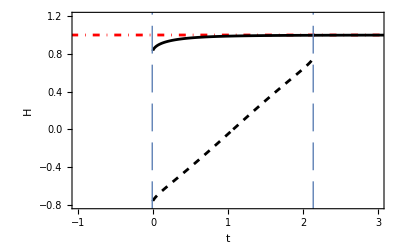

```mathematica
HT1pl=Show[HT1Bpl,ParametricPlot[{s,1},{s,-4,4},PlotStyle->{{Red,DotDashed}}],HT1Apl,ParametricPlot[{-0.01,s},{s,-5,25},PlotStyle->{{ColorData[97,1],Thick,Dashing[{0.05,0.02}]}}],ParametricPlot[{TimeBF[zcB0,Mpl],s},{s,-5,25},PlotStyle->{{ColorData[97,1],Thick,Dashing[{0.05,0.02}]}}],BaseStyle->{FontFamily->"Times",FontSize->22},LabelStyle->Directive[GrayLevel[0],FontFamily->"Times"],FrameTicks->{{Automatic,Automatic},{Automatic,None}},PlotRange->{{-1,3},{-0.80,1.2}},Axes->False,AspectRatio->1/goldenRatio]
```

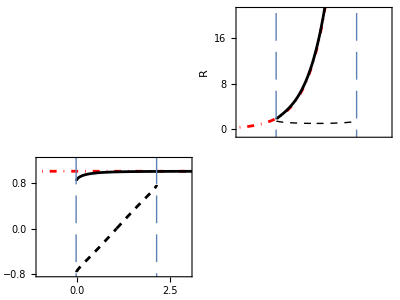

```mathematica
PlotsStackedSol=Graphics[{Inset[RT1pl,{0.0245,0.6259},{Center,Center},Scaled[{0.951,0.951}]],Inset[HT1pl,{0,0.1},{Center,Center},Scaled[{0.99995,0.99995}]]},PlotRange->{{-0.5,0.5},{-0.3,1}},ImageSize->400]
Export["Figcosmo.pdf",PlotsStackedSol];
```